## Problem 3.11 BSA, 2024

```mathematica
ClearAll["Global`*"]
Needs["VariationalMethods`"]
$Assumptions={c>0,m>0,l>0,ω>0,L>0,r>0,g>0};
```

### Lagrangian

```mathematica
A = (m*r^2)/2; 
B = (m*r^2)/4; 
e = {Sin[α[t]]*Cos[β[t]], Sin[β[t]], Cos[α[t]]*Cos[β[t]]}; 
P = (1/2)*c*L^2*e[[1]]^2 + (1/2)*c*L^2*e[[2]]^2 - g*l*m*(1 - e[[3]]); 
T = Simplify[(1/2)*A*(Derivative[1][α][t]*Sin[β[t]] + ω)^2 + (1/2)*B*(Derivative[1][α][t]^2*Cos[β[t]]^2 + Derivative[1][β][t]^2) + 
     (1/2)*l^2*m*D[e, {t}] . D[e, {t}]]; 
La = Simplify[T - P]
```

1/16 (-16 g l m (-1+Cos[α[t]] Cos[β[t]])-8 c L^2 Cos[β[t]]^2 Sin[α[t]]^2-8 c L^2 Sin[β[t]]^2+m (4 r^2 ω^2+8 r^2 ω Sin[β[t]] α'[t]+(4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]) α'[t]^2+2 (4 l^2+r^2) β'[t]^2))

#### Lagrange equations

```mathematica
pAlpha=Simplify[D[La,α'[t]]];
pBeta=Simplify[D[La,β'[t]]];
LaEq={D[D[La,α'[t]],t]-D[La,α[t]]==0,D[D[La,β'[t]],t]-D[La,β[t]]==0};
Style[TableForm[LaEq],Small]
```

1/16 (-16 g l m Cos[β[t]] Sin[α[t]]+16 c L^2 Cos[α[t]] Cos[β[t]]^2 Sin[α[t]])+1/16 m (8 r^2 ω Cos[β[t]] β'[t]-4 (4 l^2-r^2) Sin[2 β[t]] α'[t] β'[t]+2 (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]) α''[t])==0
1/16 (-16 g l m Cos[α[t]] Sin[β[t]]+16 c L^2 Cos[β[t]] Sin[β[t]]-16 c L^2 Cos[β[t]] Sin[α[t]]^2 Sin[β[t]]-m (8 r^2 ω Cos[β[t]] α'[t]-2 (4 l^2-r^2) Sin[2 β[t]] α'[t]^2))+1/4 m (4 l^2+r^2) β''[t]==0

```mathematica
SolLaEq=Simplify[Solve[LaEq[[1]]&&LaEq[[2]],{α''[t],β''[t]}]];
TableForm[SolLaEq[[1]]]
```

α''[t]→-(4 Cos[β[t]] (-2 g l m Sin[α[t]]+c L^2 Cos[β[t]] Sin[2 α[t]]+m (r^2 ω-(4 l^2-r^2) Sin[β[t]] α'[t]) β'[t]))/(m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]))
β''[t]→-(4 Cos[α[t]] (-2 g l m Sin[β[t]]+c L^2 Cos[α[t]] Sin[2 β[t]])-4 m r^2 ω Cos[β[t]] α'[t]+m (4 l^2-r^2) Sin[2 β[t]] α'[t]^2)/(2 m (4 l^2+r^2))

### Hamiltonian

```mathematica
H=Simplify[α'[t]*pAlpha+β'[t]*pBeta-La];
solP=Solve[pAlpha==pa[t]&&pBeta==pb[t],{α'[t],β'[t]}];
Ha=Simplify[H/.solP][[1]]
```

((-2 pa[t]+m r^2 ω Sin[β[t]])^2)/(m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]))+1/8 (-8 g l m-2 m r^2 ω^2+8 g l m Cos[α[t]] Cos[β[t]]+(16 pb[t]^2)/(4 l^2 m+m r^2)+4 c L^2 Cos[β[t]]^2 Sin[α[t]]^2+4 c L^2 Sin[β[t]]^2)

#### Hamilton’s equations

```mathematica
HaEq=Simplify[{D[pa[t],t]==-D[Ha,α[t]],D[α[t],t]==D[Ha,pa[t]],D[pb[t],t]==-D[Ha,β[t]],D[β[t],t]==D[Ha,pb[t]]}];
Style[TableForm[HaEq],Small]
```

pa'[t]==Cos[β[t]] (g l m-c L^2 Cos[α[t]] Cos[β[t]]) Sin[α[t]]
α'[t]==(8 pa[t]-4 m r^2 ω Sin[β[t]])/(m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]))
pb'[t]==Cos[α[t]] (g l m-c L^2 Cos[α[t]] Cos[β[t]]) Sin[β[t]]+(2 r^2 ω Cos[β[t]] (-2 pa[t]+m r^2 ω Sin[β[t]]))/(-4 l^2-3 r^2+(-4 l^2+r^2) Cos[2 β[t]])-(2 (4 l^2-r^2) (-2 pa[t]+m r^2 ω Sin[β[t]])^2 Sin[2 β[t]])/(m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]])^2)
4 pb[t]==m (4 l^2+r^2) β'[t]

#### Hamilton’s equations to Lagrange equations

```mathematica
pSolution=Solve[HaEq[[1]]&&HaEq[[2]]&&HaEq[[3]]&&HaEq[[4]],{pa'[t],pb'[t],pa[t],pb[t]}];
Ha2LaEq={Simplify[D[HaEq[[2]],t]/.pSolution][[1]],Simplify[D[HaEq[[4]],t]/.pSolution][[1]]};
Style[TableForm[Ha2LaEq],Small]
```

α''[t]==-(4 Cos[β[t]] (-2 g l m Sin[α[t]]+c L^2 Cos[β[t]] Sin[2 α[t]]+m (r^2 ω-(4 l^2-r^2) Sin[β[t]] α'[t]) β'[t]))/(m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]))
-2 Cos[α[t]] (-2 g l m Sin[β[t]]+c L^2 Cos[α[t]] Sin[2 β[t]])+2 m r^2 ω Cos[β[t]] α'[t]+m (-4 l^2+r^2) Cos[β[t]] Sin[β[t]] α'[t]^2==m (4 l^2+r^2) β''[t]

```mathematica
Simplify[Ha2LaEq/.SolLaEq]
```

{{True,True}}

### First integrals

```mathematica
FirstIntegrals[La,{α[t],β[t]},t]
```

{FirstIntegral[t]→1/16 (m (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 β[t]]) α'[t]^2+2 (-8 g l m-2 m r^2 ω^2+8 g l m Cos[α[t]] Cos[β[t]]+4 c L^2 Cos[β[t]]^2 Sin[α[t]]^2+4 c L^2 Sin[β[t]]^2+m (4 l^2+r^2) β'[t]^2))}

### Equilibrium states

```mathematica
EqStates=Simplify[{D[P,α[t]]==0,D[P,β[t]]==0}];
Simplify[Reduce[EqStates,{α[t],β[t]}],Assumptions->{c>0,m>0,l>0,ω>0,L>0,r>0,g>0}]
```

((C[1]|C[2])∈ℤ&&(((2 π C[1]==β[t]||π+2 π C[1]==β[t])&&(2 π C[2]==α[t]||π+2 π C[2]==α[t]))||((4 π C[1]==π+2 β[t]||π+4 π C[1]==2 β[t])&&(4 π C[2]==π+2 α[t]||π+4 π C[2]==2 α[t]))))||(C[1]∈ℤ&&Cos[α[t]]≠0&&(ArcCos[(g l m Sec[α[t]])/(c L^2)]+β[t]==2 π C[1]||ArcCos[(g l m Sec[α[t]])/(c L^2)]+2 π C[1]==β[t]))

```mathematica
EqEq=LaEq /.{α'[t]->0,β'[t]->0,α''[t]->0,β''[t]->0};
TableForm[EqEq]
```

1/16 (-16 g l m Cos[β[t]] Sin[α[t]]+16 c L^2 Cos[α[t]] Cos[β[t]]^2 Sin[α[t]])==0
1/16 (-16 g l m Cos[α[t]] Sin[β[t]]+16 c L^2 Cos[β[t]] Sin[β[t]]-16 c L^2 Cos[β[t]] Sin[α[t]]^2 Sin[β[t]])==0

```mathematica
Simplify[Reduce[EqEq,{α[t],β[t]}],Assumptions->{c>0,m>0,l>0,ω>0,L>0,r>0,g>0}]
```

(((2 π C[1]==α[t]&&(ArcCos[(g l m)/(c L^2)]+2 π C[2]==β[t]||ArcCos[(g l m)/(c L^2)]+β[t]==2 π C[2]))||(π+2 π C[1]==α[t]&&(ArcCos[-(g l m)/(c L^2)]+β[t]==2 π C[2]||ArcCos[-(g l m)/(c L^2)]+2 π C[2]==β[t]))||(2 π C[2]==β[t]&&(ArcCos[(g l m)/(c L^2)]+α[t]==2 π C[1]||ArcCos[(g l m)/(c L^2)]+2 π C[1]==α[t]))||((4 π C[2]==π+2 β[t]||π+4 π C[2]==2 β[t])&&(4 π C[1]==π+2 α[t]||π+4 π C[1]==2 α[t]))||((2 π C[1]==β[t]||π+2 π C[1]==β[t])&&(2 π C[2]==α[t]||π+2 π C[2]==α[t]))||(π+2 π C[1]==β[t]&&(ArcCos[-(g l m)/(c L^2)]+α[t]==2 π C[2]||ArcCos[-(g l m)/(c L^2)]+2 π C[2]==α[t])))&&(C[1]|C[2])∈ℤ)||(Tan[α[t]/2]^2≠1&&(ArcCos[(g l m Sec[α[t]])/(c L^2)]+β[t]==2 π C[1]||ArcCos[(g l m Sec[α[t]])/(c L^2)]+2 π C[1]==β[t])&&(-π+α[t])/(2 π)∉ℤ&&C[1]∈ℤ)

### Linearization

```mathematica
q={α[t],β[t],α'[t],β'[t]};
n=Length[q];
qLim=Table[q[[i]]->0,{i,1,n}];
LaLin=Sum[(D[La,q[[i]]]/.qLim) *q[[i]],{i,1,n}]+1/2*Sum[(D[La,q[[i]],q[[j]]]/.qLim)*q[[i]]*q[[j]],{i,1,n},{j,1,n}]
```

1/2 (1/16 (-16 c L^2+16 g l m) α[t]^2+1/16 (-16 c L^2+16 g l m) β[t]^2+m r^2 ω β[t] α'[t]+1/8 m (8 l^2+2 r^2) α'[t]^2+1/4 m (4 l^2+r^2) β'[t]^2)

```mathematica
LaAlmLin=LaLin+1/6*Sum[(D[La,q[[i]],q[[j]],q[[k]]]/.qLim)*q[[i]]*q[[j]]*q[[k]],{i,1,n},{j,1,n},{k,1,n}]+
	1/24*Sum[(D[La,q[[i]],q[[j]],q[[k]],q[[p]]]/.qLim)*q[[i]]*q[[j]]*q[[k]]*q[[p]],{i,1,n},{j,1,n},{k,1,n},{p,1,n}]
```

1/24 (1/16 (64 c L^2-16 g l m) α[t]^4+3/8 (32 c L^2-16 g l m) α[t]^2 β[t]^2+1/16 (64 c L^2-16 g l m) β[t]^4-2 m r^2 ω β[t]^3 α'[t]-3 m (4 l^2-r^2) β[t]^2 α'[t]^2)+1/2 (1/16 (-16 c L^2+16 g l m) α[t]^2+1/16 (-16 c L^2+16 g l m) β[t]^2+m r^2 ω β[t] α'[t]+1/8 m (8 l^2+2 r^2) α'[t]^2+1/4 m (4 l^2+r^2) β'[t]^2)

```mathematica
LaEqLin= EulerEquations[LaLin,{α[t],β[t]},t];
Collect[LaEqLin,{α[t],β[t],α'[t],β'[t], α''[t],β''[t]}]//TableForm
```

(-c L^2+g l m) α[t]-1/2 m r^2 ω β'[t]-1/4 m (4 l^2+r^2) α''[t]==0
(-c L^2+g l m) β[t]+1/2 m r^2 ω α'[t]-1/4 m (4 l^2+r^2) β''[t]==0

```mathematica
LaEqAlmLin = EulerEquations[LaAlmLin,{α[t],β[t]},t];
Style[TableForm[LaEqAlmLin],Small]
```

1/12 ((8 c L^2-2 g l m) α[t]^3+6 α[t] (-2 c L^2+2 g l m+(2 c L^2-g l m) β[t]^2)+3 m ((-2 r^2 ω+r^2 ω β[t]^2+2 (4 l^2-r^2) β[t] α'[t]) β'[t]+(-4 l^2-r^2+(4 l^2-r^2) β[t]^2) α''[t]))==0
1/12 ((8 c L^2-2 g l m) β[t]^3+6 m r^2 ω α'[t]-3 m r^2 ω β[t]^2 α'[t]+3 β[t] (-4 c L^2+4 g l m+(4 c L^2-2 g l m) α[t]^2+m (-4 l^2+r^2) α'[t]^2)-3 m (4 l^2+r^2) β''[t])==0

### Non-Dimensionalization

```mathematica
VarUpdateNonDim={t->τ/Ω,α[t]->Α[τ],β[t]->Β[τ],α'[t]->Α'[τ]*Ω,β'[t]->Β'[τ]*Ω,α''[t]->Α''[τ]*Ω^2,β''[t]->Β''[τ]*Ω^2}
```

{t→τ/Ω,α[t]→Α[τ],β[t]→Β[τ],α'[t]→Ω Α'[τ],β'[t]→Ω Β'[τ],α''[t]→Ω^2 Α''[τ],β''[t]→Ω^2 Β''[τ]}

```mathematica
(*ConvertToNonDim={c*L^2->g*m*l*Κ,ω->Sqrt[g*l*Γ]/r,l^2->r^2*Ε}*)
ConvertToNonDim1={c->σ*m*r^4*ω^2/L^2/(4*l^2+r^2), g->γ*m*r^4*ω^2/l/m/(4*l^2+r^2)}
ConvertToNonDim2={c->σ*m*r^4*ω^2/L^2/(4*l^2+r^2), g->γ*m*r^4*ω^2/l/m/(4*l^2+r^2), l^2->r^2*ϵ}
```

{c→(m r^4 σ ω^2)/(L^2 (4 l^2+r^2)),g→(r^4 γ ω^2)/(l (4 l^2+r^2))}

{c→(m r^4 σ ω^2)/(L^2 (4 l^2+r^2)),g→(r^4 γ ω^2)/(l (4 l^2+r^2)),l^2→r^2 ϵ}

#### Linear System

```mathematica
LaEqLinNonDim=LaEqLin/.VarUpdateNonDim;
LaEqLinNonDim//TableForm
```

(-c L^2+g l m) Α[τ]-1/4 m (2 r^2 ω Ω Β'[τ]+(4 l^2+r^2) Ω^2 Α''[τ])==0
(-c L^2+g l m) Β[τ]+1/4 m (2 r^2 ω Ω Α'[τ]-(4 l^2+r^2) Ω^2 Β''[τ])==0

```mathematica
OmegaUpdLin=Solve[LaEqLinNonDim[[2]]/.{Α[τ]->0,Β[τ]->0,Α'[τ]->1,Β'[τ]->1,Α''[τ]->1,Β''[τ]->1},Ω]
```

{{Ω→0},{Ω→(2 r^2 ω)/(4 l^2+r^2)}}

```mathematica
LaEqLinNonDim=LaEqLinNonDim/.OmegaUpdLin[[2]];
LaEqLinNonDim//TableForm
```

(-c L^2+g l m) Α[τ]-1/4 m ((4 r^4 ω^2 Β'[τ])/(4 l^2+r^2)+(4 r^4 ω^2 Α''[τ])/(4 l^2+r^2))==0
(-c L^2+g l m) Β[τ]+1/4 m ((4 r^4 ω^2 Α'[τ])/(4 l^2+r^2)-(4 r^4 ω^2 Β''[τ])/(4 l^2+r^2))==0

```mathematica
LaEqLinNonDim[[All,1]]=Simplify[LaEqLinNonDim[[All,1]]/(LaEqLinNonDim[[1,1]]/.{Α[τ]->0,Α''[τ]->1,Β'[τ]->0}),Assumptions->{glm-cL^2>0}];
LaEqLinNonDim//TableForm
```

((c L^2-g l m) (4 l^2+r^2) Α[τ])/(m r^4 ω^2)+Β'[τ]+Α''[τ]==0
((c L^2-g l m) (4 l^2+r^2) Β[τ])/(m r^4 ω^2)-Α'[τ]+Β''[τ]==0

```mathematica
LaEqLinNonDim[[All,1]] = Simplify[LaEqLinNonDim[[All,1]]/.ConvertToNonDim1];
LaEqLinNonDim//TableForm
```

(-γ+σ) Α[τ]+Β'[τ]+Α''[τ]==0
(-γ+σ) Β[τ]-Α'[τ]+Β''[τ]==0

```mathematica
ConvertToG=(LaEqLinNonDim[[1,1]]/.{Α[τ]->1,Α''[τ]->0,Β'[τ]->0}) -> G
```

-γ+σ→G

```mathematica
LaEqLinNonDim/.ConvertToG//TableForm
```

G Α[τ]+Β'[τ]+Α''[τ]==0
G Β[τ]-Α'[τ]+Β''[τ]==0

#### Almost Linear System

```mathematica
LaEqAlmLinNonDim=LaEqAlmLin/.VarUpdateNonDim;
Style[LaEqAlmLinNonDim//TableForm,Small]
```

1/12 ((8 c L^2-2 g l m) Α[τ]^3+6 Α[τ] (-2 c L^2+2 g l m+(2 c L^2-g l m) Β[τ]^2)+3 m (Ω (-2 r^2 ω+r^2 ω Β[τ]^2+2 (4 l^2-r^2) Ω Β[τ] Α'[τ]) Β'[τ]+Ω^2 (-4 l^2-r^2+(4 l^2-r^2) Β[τ]^2) Α''[τ]))==0
1/12 ((8 c L^2-2 g l m) Β[τ]^3+6 m r^2 ω Ω Α'[τ]-3 m r^2 ω Ω Β[τ]^2 Α'[τ]+3 Β[τ] (-4 c L^2+4 g l m+(4 c L^2-2 g l m) Α[τ]^2+m (-4 l^2+r^2) Ω^2 Α'[τ]^2)-3 m (4 l^2+r^2) Ω^2 Β''[τ])==0

```mathematica
OmegaUpdAlmLin=Simplify[Solve[LaEqAlmLinNonDim[[2]]/.{Α[τ]->0,Β[τ]->0,Α'[τ]->1,Β'[τ]->1,Α''[τ]->1,Β''[τ]->1},Ω]]
```

{{Ω→0},{Ω→(2 r^2 ω)/(4 l^2+r^2)}}

```mathematica
LaEqAlmLinNonDim=LaEqAlmLinNonDim/.OmegaUpdAlmLin[[2]];
Style[LaEqAlmLinNonDim//TableForm,Small]
```

1/12 ((8 c L^2-2 g l m) Α[τ]^3+6 Α[τ] (-2 c L^2+2 g l m+(2 c L^2-g l m) Β[τ]^2)+3 m ((2 r^2 ω (-2 r^2 ω+r^2 ω Β[τ]^2+(4 r^2 (4 l^2-r^2) ω Β[τ] Α'[τ])/(4 l^2+r^2)) Β'[τ])/(4 l^2+r^2)+(4 r^4 ω^2 (-4 l^2-r^2+(4 l^2-r^2) Β[τ]^2) Α''[τ])/((4 l^2+r^2)^2)))==0
1/12 ((8 c L^2-2 g l m) Β[τ]^3+(12 m r^4 ω^2 Α'[τ])/(4 l^2+r^2)-(6 m r^4 ω^2 Β[τ]^2 Α'[τ])/(4 l^2+r^2)+3 Β[τ] (-4 c L^2+4 g l m+(4 c L^2-2 g l m) Α[τ]^2+(4 m r^4 (-4 l^2+r^2) ω^2 Α'[τ]^2)/((4 l^2+r^2)^2))-(12 m r^4 ω^2 Β''[τ])/(4 l^2+r^2))==0

```mathematica
LaEqAlmLinNonDim = Simplify[Simplify[LaEqAlmLinNonDim /. ConvertToNonDim2] /. ConvertToNonDim2];
Style[TableForm[LaEqAlmLinNonDim], Small]
```

(1+4 ϵ) Α[τ] (-6 γ+6 σ+(γ-4 σ) Α[τ]^2+3 (γ-2 σ) Β[τ]^2)==3 (-2-8 ϵ+(1+4 ϵ) Β[τ]^2+4 (-1+4 ϵ) Β[τ] Α'[τ]) Β'[τ]+6 (-1-4 ϵ+(-1+4 ϵ) Β[τ]^2) Α''[τ]
Β[τ] (3 (1+4 ϵ) (γ-2 σ) Α[τ]^2+(1+4 ϵ) (γ-4 σ) Β[τ]^2+3 (1+4 ϵ) Β[τ] Α'[τ]-6 ((1+4 ϵ) (γ-σ)+(1-4 ϵ) Α'[τ]^2))==6 (1+4 ϵ) (Α'[τ]-Β''[τ])

#### Non-Linear System

```mathematica
LaEqNonDim=LaEq/.VarUpdateNonDim;
Style[LaEqNonDim//TableForm,Small]
```

1/16 (-16 g l m Cos[Β[τ]] Sin[Α[τ]]+16 c L^2 Cos[Α[τ]] Cos[Β[τ]]^2 Sin[Α[τ]])+1/16 m (8 r^2 ω Ω Cos[Β[τ]] Β'[τ]-4 (4 l^2-r^2) Ω^2 Sin[2 Β[τ]] Α'[τ] Β'[τ]+2 Ω^2 (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 Β[τ]]) Α''[τ])==0
1/16 (-16 g l m Cos[Α[τ]] Sin[Β[τ]]+16 c L^2 Cos[Β[τ]] Sin[Β[τ]]-16 c L^2 Cos[Β[τ]] Sin[Α[τ]]^2 Sin[Β[τ]]-m (8 r^2 ω Ω Cos[Β[τ]] Α'[τ]-2 (4 l^2-r^2) Ω^2 Sin[2 Β[τ]] Α'[τ]^2))+1/4 m (4 l^2+r^2) Ω^2 Β''[τ]==0

```mathematica
OmegaUpd=Simplify[Solve[LaEqNonDim[[2]]/.{Α[τ]->0,Β[τ]->0,Α'[τ]->1,Β'[τ]->1,Α''[τ]->1,Β''[τ]->1},Ω]]
```

{{Ω→0},{Ω→(2 r^2 ω)/(4 l^2+r^2)}}

```mathematica
LaEqNonDim=LaEqNonDim/.OmegaUpd[[2]];
Style[LaEqNonDim//TableForm,Small]
```

1/16 (-16 g l m Cos[Β[τ]] Sin[Α[τ]]+16 c L^2 Cos[Α[τ]] Cos[Β[τ]]^2 Sin[Α[τ]])+1/16 m ((16 r^4 ω^2 Cos[Β[τ]] Β'[τ])/(4 l^2+r^2)-(16 r^4 (4 l^2-r^2) ω^2 Sin[2 Β[τ]] Α'[τ] Β'[τ])/((4 l^2+r^2)^2)+(8 r^4 ω^2 (4 l^2+3 r^2+(4 l^2-r^2) Cos[2 Β[τ]]) Α''[τ])/((4 l^2+r^2)^2))==0
1/16 (-16 g l m Cos[Α[τ]] Sin[Β[τ]]+16 c L^2 Cos[Β[τ]] Sin[Β[τ]]-16 c L^2 Cos[Β[τ]] Sin[Α[τ]]^2 Sin[Β[τ]]-m ((16 r^4 ω^2 Cos[Β[τ]] Α'[τ])/(4 l^2+r^2)-(8 r^4 (4 l^2-r^2) ω^2 Sin[2 Β[τ]] Α'[τ]^2)/((4 l^2+r^2)^2)))+(m r^4 ω^2 Β''[τ])/(4 l^2+r^2)==0

```mathematica
LaEqNonDim = Simplify[Simplify[LaEqNonDim /. ConvertToNonDim2] /. ConvertToNonDim2];
Style[TableForm[LaEqNonDim], Small]
```

2 (1+4 ϵ) Cos[Β[τ]] (-γ+σ Cos[Α[τ]] Cos[Β[τ]]) Sin[Α[τ]]+(3+4 ϵ+(-1+4 ϵ) Cos[2 Β[τ]]) Α''[τ]==2 Cos[Β[τ]] (-1-4 ϵ+2 (-1+4 ϵ) Sin[Β[τ]] Α'[τ]) Β'[τ]
2 (1+4 ϵ) Cos[Β[τ]] Α'[τ]==(-1+4 ϵ) Sin[2 Β[τ]] Α'[τ]^2+(1+4 ϵ) (Cos[Α[τ]] (-2 γ Sin[Β[τ]]+σ Cos[Α[τ]] Sin[2 Β[τ]])+2 Β''[τ])

### Stability domain

```mathematica
LaEqLinNonDim//TableForm
```

(-γ+σ) Α[τ]+Β'[τ]+Α''[τ]==0
(-γ+σ) Β[τ]-Α'[τ]+Β''[τ]==0

#### Characteristic equation

```mathematica
X={Α[τ],Β[τ]};
EulerConvert=Flatten[Table[D[X[[i]],{τ,j}]->D[Subscript[a,i]*Exp[λ*τ],{τ,j}],{i,2},{j,0,2}]]
```

{Α[τ]→ⅇ^(λ τ) a_1,Α'[τ]→ⅇ^(λ τ) λ a_1,Α''[τ]→ⅇ^(λ τ) λ^2 a_1,Β[τ]→ⅇ^(λ τ) a_2,Β'[τ]→ⅇ^(λ τ) λ a_2,Β''[τ]→ⅇ^(λ τ) λ^2 a_2}

```mathematica
CharTemp=Simplify[(LaEqLinNonDim[[All,1]]/.EulerConvert)/Exp[λ*τ]];
CharM=Table[D[CharTemp[[i]],Subscript[a,j]],{i,2},{j,2}];
CharM//MatrixForm
```

(-γ+λ^2+σ | λ
-λ | -γ+λ^2+σ)

```mathematica
CharEq=Det[CharM]==0
```

γ^2+λ^2-2 γ λ^2+λ^4-2 γ σ+2 λ^2 σ+σ^2==0

```mathematica
EigVal=Flatten[Solve[CharEq,λ]]
```

{λ→-(√(-1+2 γ-2 σ-√(1-4 γ+4 σ)))/(√2),λ→(√(-1+2 γ-2 σ-√(1-4 γ+4 σ)))/(√2),λ→-√(-1/2+γ-σ+1/2 √(1-4 γ+4 σ)),λ→√(-1/2+γ-σ+1/2 √(1-4 γ+4 σ))}

#### Stability condition for the biquadrate equation

```mathematica
CharEq1=Collect[CharEq/.{λ->Sqrt[ξ]},ξ]
```

γ^2+ξ^2-2 γ σ+σ^2+ξ (1-2 γ+2 σ)==0

```mathematica
BiSol=Flatten[Solve[CharEq1,ξ]]
```

{ξ→1/2 (-1+2 γ-2 σ-√(1-4 γ+4 σ)),ξ→1/2 (-1+2 γ-2 σ+√(1-4 γ+4 σ))}

```mathematica
StabDomainCond=Apply[BitAnd,Table[Negative[ξ/.BiSol[[i]]],{i,Length[BiSol]}]]
```

BitAnd[Negative[-1+2 γ-2 σ-√(1-4 γ+4 σ)],Negative[-1+2 γ-2 σ+√(1-4 γ+4 σ)]]

#### Stability domain

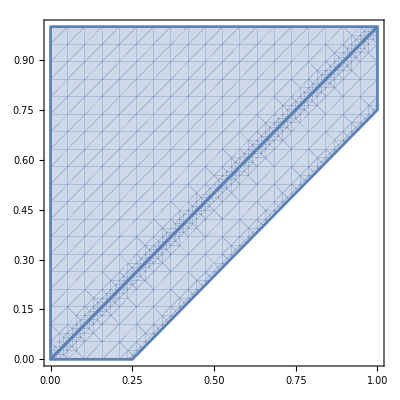

```mathematica
RegionPlot[StabDomainCond,{γ,0,1},{σ,0,1}]
```

#### Eigenvalues on the complex plane

```mathematica
Animate[ComplexListPlot[Table[(λ/.EigVal[[i]])/.{γ->(1-G)/2,σ->(G+1)/2},{i,Length[EigVal]}], PlotRange->{{-1.5,1.5},{-1.5,1.5}}, 
	PlotStyle->{PointSize[Large]},AxesLabel->{"Re","Im"}],{G, -0.255, 0.1, Appearance -> "Labeled"}, AnimationRunning -> False]
```

### Crossing the border

```mathematica
LaEqLinNonDimG = LaEqLinNonDim /. ConvertToG;
LaEqLinNonDimG //TableForm
```

G Α[τ]+Β'[τ]+Α''[τ]==0
G Β[τ]-Α'[τ]+Β''[τ]==0

#### Characteristic equation

```mathematica
CharTempG = Simplify[(LaEqLinNonDimG[[All, 1]] /. EulerConvert) / Exp[λ * τ]];
CharMG = Table[D[CharTempG[[i]], Subscript[a, j]], {i, 2}, {j, 2}];
Print["S = ", MatrixForm[CharMG]]
```

S = (G+λ^2 | λ
-λ | G+λ^2)

```mathematica
CharEqG = Collect[Det[CharMG] == 0, λ]
```

G^2+(1+2 G) λ^2+λ^4==0

```mathematica
DiscBi = Discriminant[CharEqG[[1]] /. {λ^2 -> χ, λ^4 -> χ^2}, χ];
Print["D = ", DiscBi]
```

D = 1+4 G

```mathematica
EigValG = Flatten[Solve[CharEqG, λ]]
```

{λ→-(√(-1-2 G-√(1+4 G)))/(√2),λ→(√(-1-2 G-√(1+4 G)))/(√2),λ→-(√(-1-2 G+√(1+4 G)))/(√2),λ→(√(-1-2 G+√(1+4 G)))/(√2)}

#### Border eigenvalues

```mathematica
Print[Subscript[λ, "G=0"], " = ", EigValG[[All, 2]] /. {G -> 0}]
Print[Subscript[λ, "G=-1/4"], " = ", EigValG[[All, 2]] /. Solve[DiscBi == 0, G][[1]]]
```

λ_(G=0) = {-ⅈ,ⅈ,0,0}

λ_(G=-1/4) = {-ⅈ/2,ⅈ/2,-ⅈ/2,ⅈ/2}

#### Normal form of the system

```mathematica
M = {{0, -1, -G, 0}, {1, 0, 0, -G}, {1, 0, 0, 0}, {0, 1, 0, 0}};
Print["M = ", MatrixForm[M]]
```

M = (0 | -1 | -G | 0
1 | 0 | 0 | -G
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
JM1 = JordanDecomposition[M /. {G -> 0}][[2]];
JM2 = JordanDecomposition[M /. {G -> -1/4}][[2]];
Print[Subscript[J, "G=0"], " = ", MatrixForm[JM1], ",   ", Subscript[J, "G=-1/4"], " = ", MatrixForm[JM2]]
```

J_(G=0) = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),   J_(G=-1/4) = (-ⅈ/2 | 1 | 0 | 0
0 | -ⅈ/2 | 0 | 0
0 | 0 | ⅈ/2 | 1
0 | 0 | 0 | ⅈ/2)

#### Conclusion on stability

```mathematica
Print["1) G < -1/4     : Exponential divergence           [exp(t) * sin(ω * t)]"]
Print["2) G = -1/4     : Weak polynomial divergence       [t * sin(ω * t)]"]
Print["3) -1/4 < G < 0 : Harmonic oscillations            [sin(ω * t)]"]
Print["4) G = 0        : Harmonic oscillations with shift [C + sin(ω * t)]"]
Print["4) G > 0        : Harmonic oscillations            [sin(ω * t)]"]
```

1) G < -1/4     : Exponential divergence           [exp(t) * sin(ω * t)]

2) G = -1/4     : Weak polynomial divergence       [t * sin(ω * t)]

3) -1/4 < G < 0 : Harmonic oscillations            [sin(ω * t)]

4) G = 0        : Harmonic oscillations with shift [C + sin(ω * t)]

4) G > 0        : Harmonic oscillations            [sin(ω * t)]

### Solutions planes. Configuration space. Phase space

```mathematica
X = {Η[τ], Θ[τ], Α[τ], Β[τ]};
X0 = Thread[(X /. τ -> 0) == {0.01, 0.01, 0.01, 0.01}];
ConvertToX = {Α''[τ] -> Η'[τ], Α'[τ] -> Η[τ], Β''[τ] -> Θ'[τ], Β'[τ] -> Θ[τ]};
(*ToTor[x_] := {(x[[4]] * Cos[x[[2]]] + x[[3]]) * Sin[x[[1]]], (x[[4]] * Cos[x[[2]]] + x[[3]]) * Cos[x[[1]]], x[[4]] * Sin[x[[2]]]};*)
ToTor[x_] := {x[[3]] * (6 + x[[4]] / Sqrt[x[[3]]^2 + x[[1]]^2]), x[[1]] * (6 + x[[4]] / Sqrt[x[[3]]^2 + x[[1]]^2]), x[[2]]};
```

```mathematica
LinSys = Union[LaEqLinNonDim /. ConvertToX, {Α'[τ] == Η[τ], Β'[τ] == Θ[τ]}];
AlmLinSys = Union[LaEqAlmLinNonDim /. ConvertToX, {Α'[τ] == Η[τ], Β'[τ] == Θ[τ]}];
NonLinSys = Union[LaEqNonDim /. ConvertToX, {Α'[τ] == Η[τ], Β'[τ] == Θ[τ]}];
```

#### Linear system

```mathematica
SolutionTor[g_, t_] := (
	ConvertToGT = {γ -> (1 - g) / 2, σ -> (g + 1) / 2, ϵ -> 4};
	SolLin = NDSolveValue[Union[LinSys /. ConvertToGT, X0], X, {τ, 0, t}];
	r = Sqrt[SolLin[[2]]^2 + SolLin[[4]]^2];
	
	p1 = ParametricPlot3D[ToTor[SolLin], {τ, 0, t}, PlotStyle -> {Blue}, PlotLegends -> Placed[{"Phase Space"}, Bottom], PlotRange->All];
	p2 = ParametricPlot3D[ToTor[{SolLin[[1]], r * Sin[θ], SolLin[[3]], r * Cos[θ]}], {τ, 0, t}, {θ, 0, 2*Pi}, PlotStyle -> {Green, Opacity[0.3]}, 
		PlotPoints -> 10];
	p3 = Plot[SolLin[[3]], {τ, 0, t}, AxesLabel -> {τ, Α[τ]}, GridLines -> Automatic, AspectRatio -> 1/2];
	p4 = Plot[SolLin[[4]], {τ, 0, t}, AxesLabel -> {τ, Β[τ]}, GridLines -> Automatic, AspectRatio -> 1/2];
	
	GraphicsRow[{Show[p1, p2, SphericalRegion -> True, ImageSize -> Full], GraphicsColumn[{p3, p4}, ImageSize -> Full]}]
);
Animate[SolutionTor[G, T], {G, -0.2505, 0.1, Appearance -> "Labeled"}, {T, 1, 100, Appearance -> "Labeled"}, AnimationRunning -> False]
```

#### Full analysis

```mathematica
Solution[g_, t_] := (
	ConvertToGT = {γ -> (1 - g) / 2, σ -> (g + 1) / 2, ϵ -> 4};
	
	SolLin = NDSolveValue[Union[LinSys /. ConvertToGT, X0], X, {τ, 0, t}];
	SolAlmLin = NDSolveValue[Union[AlmLinSys /. ConvertToGT, X0], X, {τ, 0, t}];
	SolNonLin = NDSolveValue[Union[NonLinSys /. ConvertToGT, X0], X, {τ, 0, t}];
	r = Sqrt[SolLin[[2]]^2 + SolLin[[4]]^2];
	
	pp1 = ParametricPlot3D[{ToTor[SolLin], ToTor[SolAlmLin], ToTor[SolNonLin]}, {τ, 0, t}, 
		PlotStyle -> {Blue, Red, Darker[Green]}, PlotLegends -> Placed[{"Lin", "AlmLin", "NonLin"}, Bottom], PlotRange -> All];
	pp2 = ParametricPlot3D[ToTor[{SolLin[[1]], r * Sin[θ], SolLin[[3]], r * Cos[θ]}], {τ, 0, t}, {θ, 0, 2*Pi}, PlotStyle -> {Gray, Opacity[0.1]}];
	
	p1 = Plot[{SolLin[[3]], SolAlmLin[[3]], SolNonLin[[3]]}, {τ, 0, t}, AxesLabel -> {τ, Α[τ]}, GridLines -> Automatic, PlotRange -> All, 
		PlotStyle -> {Blue, Red, Darker[Green]}, PlotLegends -> Placed[{"Lin", "AlmLin", "NonLin"}, Bottom], ImageSize -> Full, AspectRatio -> 9/10];
	p2 = Plot[{SolLin[[4]], SolAlmLin[[4]], SolNonLin[[4]]}, {τ, 0, t}, AxesLabel -> {τ, Β[τ]}, GridLines -> Automatic, PlotRange -> All,
		PlotStyle -> {Blue, Red, Darker[Green]}, PlotLegends -> Placed[{"Lin", "AlmLin", "NonLin"}, Bottom], ImageSize -> Full, AspectRatio -> 9/10];
	p3 = ComplexListPlot[Table[(λ /. EigVal[[i]]) /. ConvertToGT, {i, Length[EigVal]}], PlotRange -> {{-2, 2}, {-2, 2}}, 
		PlotStyle -> {PointSize[Large], Red}, AxesLabel -> {"Re", "Im"}];
	p4 = Show[RegionPlot[StabDomainCond, {γ, 0, 1}, {σ, 0, 1}], Graphics[{Red, PointSize[Large], Point[{(1 - g) / 2, (1 + g) / 2}]}]];
	p5 = Show[pp1, pp2, SphericalRegion -> True, ImageSize -> Full];
	p6 = ParametricPlot[{{SolLin[[3]], SolLin[[4]]}, {SolAlmLin[[3]], SolAlmLin[[4]]}, {SolNonLin[[3]], SolNonLin[[4]]}}, {τ, 0, t}, 
		AxesLabel -> {Α, Β}, GridLines -> Automatic, PlotRange -> All, PlotStyle -> {Blue, Red, Darker[Green]}, 
		PlotLegends -> Placed[{"Lin", "AlmLin", "NonLin"}, Bottom], ImageSize -> Full, AspectRatio -> 9/10];
	
	GraphicsGrid[{{p5, p3, p1}, {p6, p4, p2}}, ImageSize -> Large]
);
Animate[Solution[G, T], {G, -0.33, 0.1, Appearance -> "Labeled"}, {T, 1, 100, Appearance -> "Labeled"}, AnimationRunning -> False]
```